## Preamble

```mathematica
δn[n_,H_,q_,d_]:=Table[Sum[((1+(ⅈ(2-q.n))/(d(1-q.n))(1-Exp[-ⅈ d(1-q.n)]))n⟦i⟧-(1+ⅈ/(d(1-q.n))(1-Exp[-ⅈ d(1-q.n)]))q⟦i⟧)(H⟦j,k⟧n⟦j⟧n⟦k⟧)/(2(1-q.n)),{j,1,3},{k,1,3}]-Sum[(1/2+ⅈ/(d(1-q.n))(1-Exp[-ⅈ d(1-q.n)]))H⟦i,j⟧n⟦j⟧,{j,1,3}],{i,1,3}]
δn[n_,H_,q_]:=Table[Sum[Sum[(n⟦i⟧-q⟦i⟧)(H⟦j,k⟧n⟦j⟧n⟦k⟧)/(2(1-q.n)),{k,1,3}]-1/2 H⟦i,j⟧n⟦j⟧,{j,1,3}],{i,1,3}]
```

```mathematica
SphericalIntegral[Integrand_,nSamplePoints_,nIntPoints_]:=Block[{IntegrandFunc,GaussLegendreNodesSampling,GaussLegendreNodesInt,GaussLegendreWeightsInt,IntegrandVals,FunctionVals},
IntegrandFunc=Compile[{{Θ,_Real},{θ,_Real},{ϕ,_Real}},Evaluate@Integrand];

GaussLegendreNodesSampling=Join[{-1},Sort[N[x/.Solve[LegendreP[nSamplePoints-2,x]==0]]],{1}];
GaussLegendreNodesInt=Sort[N[x/.Solve[LegendreP[nIntPoints,x]==0]]];
GaussLegendreWeightsInt=ParallelTable[2/((1-GaussLegendreNodesInt⟦i⟧^2)LegendrePDiff[nIntPoints,GaussLegendreNodesInt⟦i⟧]^2),{i,1,nIntPoints}];

IntegrandVals=ParallelTable[N[IntegrandFunc[ArcCos[GaussLegendreNodesSampling⟦i⟧],ArcCos[GaussLegendreNodesInt⟦j⟧],(k-(1/2))π/nIntPoints]],{i,1,nSamplePoints},{j,1,nIntPoints},{k,1,2nIntPoints}];

FunctionVals=Reverse@Table[{ArcCos[GaussLegendreNodesSampling⟦i⟧],ParallelSum[GaussLegendreWeightsInt⟦j⟧ IntegrandVals⟦i,j,k⟧,{j,1,nIntPoints},{k,1,2nIntPoints}]},{i,1,nSamplePoints}];

AbsMaxVal=Max@Abs@FunctionVals⟦All,2⟧;
FunctionVals⟦All,2⟧=FunctionVals⟦All,2⟧/AbsMaxVal;

Return[FunctionVals];]
```

```mathematica
n={0,0,1};
Subscript[n, x]={1,0,0};
Subscript[n, y]={0,1,0};
m={Sin[Θ],0,Cos[Θ]};
Subscript[m, θ]={Cos[Θ],0,-Sin[Θ]};
Subscript[m, ϕ]={0,1,0};
q=(1-ϵ){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
```

```mathematica
R=Simplify[RotationMatrix[-θ,{0,1,0}].RotationMatrix[-ϕ,{0,0,1}]];
```

```mathematica
y1=100;
y2=100;
```

```mathematica
epsilons=Reverse@Range[-0.5,0.5,0.01];
```

## Tensorial Modes Correlation Curves

```mathematica
Htensorial=Transpose[R].({{1, 1, 0}, {1, -1, 0}, {0, 0, 0}}).R;

TensorialxθPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Htensorial,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Htensorial,q,y2]]];
Integrandxθ=(Deltan.{1,0,0})(Deltam.{Cos[Θ],0,-Sin[Θ]});
SphericalIntegral[Integrandxθ,3,100],{i,1,Length[epsilons]}];

TensorialyϕPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Htensorial,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Htensorial,q,y2]]];
Integrandyϕ=(Deltan.{0,1,0})(Deltam.{0,1,0});
SphericalIntegral[Integrandyϕ,3,100],{i,1,Length[epsilons]}];
```

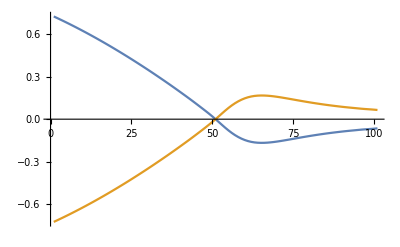

```mathematica
ListPlot[{TensorialxθPlots[[All,3,2]],TensorialyϕPlots[[All,3,2]]},Joined->True,PlotRange->All]
```

## Scalar Transverse Modes Correlation Curves

```mathematica
Hscalar=Transpose[R].({{1, 0, 0}, {0, 1, 0}, {0, 0, 0}}).R;

ScalarxθPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hscalar,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hscalar,q,y2]]];
Integrandxθ=(Deltan.{1,0,0})(Deltam.{Cos[Θ],0,-Sin[Θ]});
SphericalIntegral[Integrandxθ,3,100],{i,1,Length[epsilons]}];

ScalaryϕPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hscalar,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hscalar,q,y2]]];
Integrandyϕ=(Deltan.{0,1,0})(Deltam.{0,1,0});
SphericalIntegral[Integrandyϕ,3,100],{i,1,Length[epsilons]}];
```

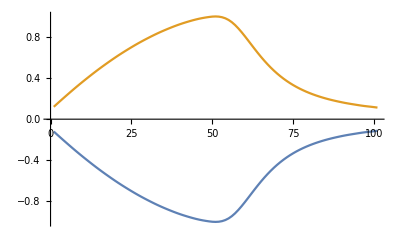

```mathematica
ListPlot[{ScalarxθPlots[[All,3,2]],ScalaryϕPlots[[All,3,2]]},Joined->True,PlotRange->All]
```

## Vectorial Modes Correlation Curves

```mathematica
Hvectorial=Transpose[R].({{0, 0, 1}, {0, 0, 1}, {1, 1, 0}}).R;

VectorialxθPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hvectorial,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hvectorial,q,y2]]];
Integrandxθ=(Deltan.{1,0,0})(Deltam.{Cos[Θ],0,-Sin[Θ]});
SphericalIntegral[Integrandxθ,3,100],{i,1,Length[epsilons]}];

VectorialyϕPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hvectorial,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hvectorial,q,y2]]];
Integrandyϕ=(Deltan.{0,1,0})(Deltam.{0,1,0});
SphericalIntegral[Integrandyϕ,3,100],{i,1,Length[epsilons]}];
```

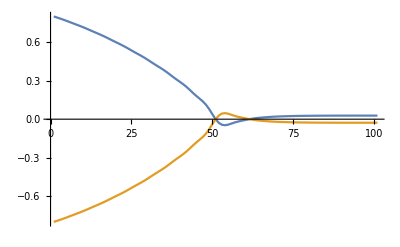

```mathematica
ListPlot[{VectorialxθPlots[[All,3,2]],VectorialyϕPlots[[All,3,2]]},Joined->True,PlotRange->All]
```

## Longitudinal Mode Correlation Curves

```mathematica
Hlongitudinal=√2 Transpose[R].({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}}).R;

LongitudinalxθPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hlongitudinal,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hlongitudinal,q,y2]]];
Integrandxθ=(Deltan.{1,0,0})(Deltam.{Cos[Θ],0,-Sin[Θ]});
SphericalIntegral[Integrandxθ,3,100],{i,1,Length[epsilons]}];

LongitudinalyϕPlots=Table[
q=(1-epsilons⟦i⟧){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
Deltan=Simplify[ComplexExpand[Re[δn[n,Hlongitudinal,q,y1]]],Assumptions->{0≤Θ≤π,0≤θ≤π,0≤ϕ≤2π}];
Deltam=ComplexExpand[Re[δn[m,Hlongitudinal,q,y2]]];
Integrandyϕ=(Deltan.{0,1,0})(Deltam.{0,1,0});
SphericalIntegral[Integrandyϕ,3,100],{i,1,Length[epsilons]}];
```

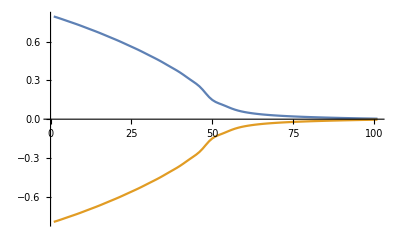

```mathematica
ListPlot[{LongitudinalxθPlots[[All,3,2]],LongitudinalyϕPlots[[All,3,2]]},Joined->True,PlotRange->All]
```

```mathematica
Table2=Transpose[{LongitudinalyϕPlots[[1,All,1]],LongitudinalyϕPlots[[1,All,2]],LongitudinalyϕPlots[[2,All,2]], LongitudinalyϕPlots[[3,All,2]],LongitudinalyϕPlots[[4,All,2]]}];
```

```mathematica
Export["table1.dat",Table2]
```

table1.dat